```mathematica
Convolve[UnitStep[x-1]*UnitStep[3-x],UnitStep[x+5]*UnitStep[-1-x],x,t]
∫_1^3 UnitStep[t-T+3]*UnitStep[1-t+T]ⅆT
```

```mathematica
Convolve[E^(-a*x)*UnitStep[x],E^(-a*x)*UnitStep[x],x,t]
```

```mathematica
Convolve[a*x+b,UnitStep[x]*UnitStep[1-x]*4/3-1/3*DiracDelta[x-2],x,t]
```

b+a ((2-t)/3+4/3 (-1/2+t))

```mathematica
Simplify[b+a ((2-t)/3+4/3 (-1/2+t))]
```

b+a t

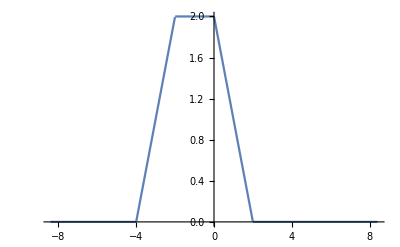

```mathematica
Plot[Piecewise[{{2,-2≤t≤0},{2-t,0<t≤2},{4+t,-4≤t<-2}},0],{t,-8.4,8.4}]
```